{dx+x,dy+y,dz+z}

sol = {x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2)),z→0}

x[a], y[a]

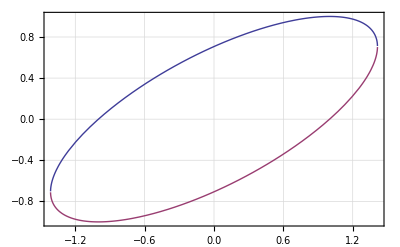

f = (-a+x+y+z)^2+(-1+x^2+y^2+z^2)^2

grad

grad = (0
0
0)

hh = (6+4 a √(2-a^2) | -2+4 a^2 | 2
-2+4 a^2 | 6-4 a √(2-a^2) | 2
2 | 2 | 2)

eVal = (0
7-√(1+16 a^2)
7+√(1+16 a^2))

eVal

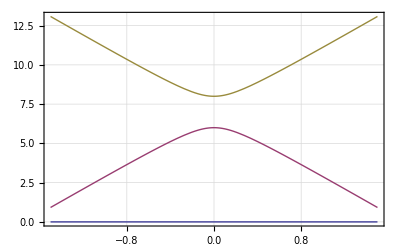

```mathematica
ClearAll["Global`*"];
coord={x,y,z};
dcoord={dx,dy,dz};
coordNew=coord+dcoord;

aMax=1.5;
plotOptions={PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Thick};

Mk[coordVec_?VectorQ,level_?IntegerQ]:=Sum[coordVec[[ii]]^level,{ii,1,Length[coordVec]}];

M1=x+y+z;
M2=x^2+y^2+z^2;

sol=Solve[{M1==a,M2==1,z==0},coord][[2]];
Print["sol = ", sol];

rule=sol;

Print["x[a], y[a]"];
xx[a_]=x/. sol;
yy[a_]=y/. sol;
Print[Plot[{xx[a],yy[a]},{a,-aMax,aMax},Evaluate[plotOptions]]];

func[a_,x_,y_,z_]=(M1-a)^2+(M2-1)^2;
f=func[a,x,y,z];
Print["f = ",f];

Print["grad"];
grad=Simplify[Table[D[f,coord[[ii]]],{ii,1,3}]/.rule];
Print["grad = ",grad//MatrixForm];

hh=Simplify[Table[D[D[f,coord[[ii]]],coord[[jj]]],{ii,1,3},{jj,1,3}]/.rule];
Print["hh = ",hh//MatrixForm];


eVal=Simplify[Eigenvalues[hh]];
Print["eVal = ",eVal//MatrixForm];
eValFunc[a_]=eVal;

Print["eVal"];
Print[Plot[{eValFunc[a][[1]],eValFunc[a][[2]],eValFunc[a][[3]]},{a,-aMax,aMax},Evaluate[plotOptions]]];

(*
Print["f[a]"];
Print[Plot[funcVal[a],{a,-aMax,aMax},Evaluate[plotOptions]]];


*)
```